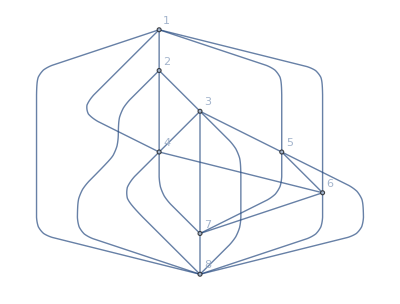
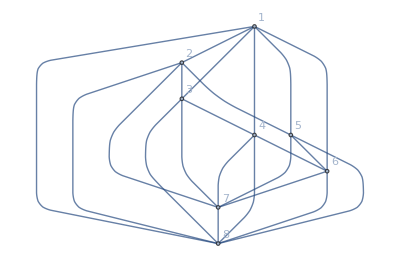
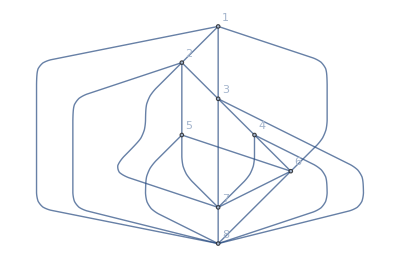
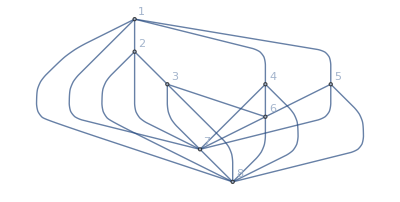
{-Graphics-{3,{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3}},-Graphics-{4,{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7}},-Graphics-{2,{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7}},-Graphics-{2,{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3}}}

```mathematica
Select[Table[With[{g=CompleteGraph[8],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
If[ChromaticPolynomial[res,4]==0,
Labeled[Graph[res,VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"],{EdgeCount[res]-(VertexCount[res]*3-6),edges}]
]
]
],
{edges,{{4<->5,3<->6,2<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->7,1<->5,1<->4},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->2},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->4},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},{4<->5,3<->5,3<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->4,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6}}}
],#=!=Null&]
```

```mathematica
RemoveEdges[edges_]:=Block[{g=EdgeDelete[CompleteGraph[8],edges],nonedges},
nonedges=EdgeList[g];
Select[
Table[
With[{h=Graph[EdgeDelete[g,e],VertexLabels->"Name"]},
{Labeled[Graph[g,GraphHighlight->e,GraphHighlightStyle->"Thick", VertexLabels->"Name"],EdgeCount[h]],ChromaticPolynomial[h,4],PlanarGraphQ[h],e}
]
,{e,Subsets[nonedges,{10-Length[edges]}]}
],
#[[3]]&]
]
```

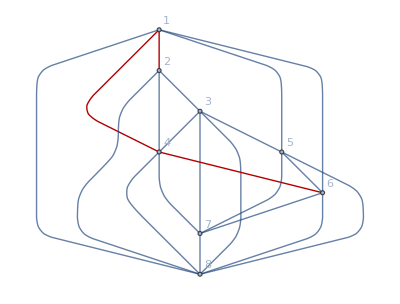

```mathematica
Graph[-Graphics-,GraphHighlight->{1<->2,1<->4,4<->6}]
```

```mathematica
RemoveEdges[{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3}]
```

{{-Graphics-18,24,True,{1<->2,1<->4,3<->5}},{-Graphics-18,24,True,{1<->2,1<->4,4<->6}},{-Graphics-18,96,True,{1<->2,1<->4,7<->8}},{-Graphics-18,24,True,{1<->2,1<->5,3<->5}},{-Graphics-18,24,True,{1<->2,1<->5,5<->6}},{-Graphics-18,96,True,{1<->2,1<->5,7<->8}},{-Graphics-18,24,True,{1<->2,3<->5,5<->7}},{-Graphics-18,96,True,{1<->2,3<->5,6<->8}},{-Graphics-18,120,True,{1<->2,6<->8,7<->8}},{-Graphics-18,24,True,{1<->5,1<->6,3<->5}},{-Graphics-18,24,True,{1<->5,1<->6,4<->6}},{-Graphics-18,24,True,{1<->5,1<->6,5<->6}},{-Graphics-18,96,True,{1<->5,1<->6,7<->8}},{-Graphics-18,24,True,{1<->5,2<->3,3<->4}},{-Graphics-18,24,True,{1<->5,2<->3,3<->5}},{-Graphics-18,24,True,{1<->5,2<->3,5<->6}},{-Graphics-18,96,True,{1<->5,2<->3,7<->8}},{-Graphics-18,24,True,{1<->5,3<->5,3<->7}},{-Graphics-18,120,True,{1<->5,3<->5,4<->8}},{-Graphics-18,120,True,{1<->5,4<->8,5<->6}},{-Graphics-18,72,True,{1<->5,4<->8,7<->8}},{-Graphics-18,24,True,{1<->5,5<->6,6<->7}},{-Graphics-18,24,True,{2<->3,3<->4,4<->7}},{-Graphics-18,96,True,{2<->3,3<->4,6<->8}},{-Graphics-18,24,True,{2<->3,3<->5,5<->7}},{-Graphics-18,96,True,{2<->3,3<->5,6<->8}},{-Graphics-18,120,True,{2<->3,6<->8,7<->8}},{-Graphics-18,24,True,{3<->5,3<->7,4<->7}},{-Graphics-18,24,True,{3<->5,3<->7,5<->7}},{-Graphics-18,96,True,{3<->5,3<->7,6<->8}},{-Graphics-18,120,True,{3<->5,4<->8,5<->7}},{-Graphics-18,72,True,{3<->5,4<->8,6<->8}},{-Graphics-18,24,True,{3<->5,5<->7,6<->7}},{-Graphics-18,72,True,{4<->8,6<->8,7<->8}}}

```mathematica
RemoveEdges2[edges_]:=Block[{g=EdgeDelete[CompleteGraph[8],edges],nonedges},
nonedges=EdgeList[g];
Map[#[[4]]&,
Select[
Table[
With[{h=Graph[EdgeDelete[g,e],VertexLabels->"Name"]},
{Labeled[Graph[g,GraphHighlight->e,GraphHighlightStyle->"Thick", VertexLabels->"Name"],EdgeCount[h]],ChromaticPolynomial[h,4],PlanarGraphQ[h],e}
]
,{e,Subsets[nonedges,{10-Length[edges]}]}
],
#[[3]]&]
]
]
```

```mathematica
cross=RemoveEdges2[{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3}]
```

{{1<->2,1<->4,3<->5},{1<->2,1<->4,4<->6},{1<->2,1<->4,7<->8},{1<->2,1<->5,3<->5},{1<->2,1<->5,5<->6},{1<->2,1<->5,7<->8},{1<->2,3<->5,5<->7},{1<->2,3<->5,6<->8},{1<->2,6<->8,7<->8},{1<->5,1<->6,3<->5},{1<->5,1<->6,4<->6},{1<->5,1<->6,5<->6},{1<->5,1<->6,7<->8},{1<->5,2<->3,3<->4},{1<->5,2<->3,3<->5},{1<->5,2<->3,5<->6},{1<->5,2<->3,7<->8},{1<->5,3<->5,3<->7},{1<->5,3<->5,4<->8},{1<->5,4<->8,5<->6},{1<->5,4<->8,7<->8},{1<->5,5<->6,6<->7},{2<->3,3<->4,4<->7},{2<->3,3<->4,6<->8},{2<->3,3<->5,5<->7},{2<->3,3<->5,6<->8},{2<->3,6<->8,7<->8},{3<->5,3<->7,4<->7},{3<->5,3<->7,5<->7},{3<->5,3<->7,6<->8},{3<->5,4<->8,5<->7},{3<->5,4<->8,6<->8},{3<->5,5<->7,6<->7},{4<->8,6<->8,7<->8}}

```mathematica
EdgeList[-Graphics-]
```

{1<->2,1<->4,1<->5,1<->6,1<->8,2<->3,2<->4,2<->8,3<->4,3<->5,3<->7,3<->8,4<->6,4<->7,4<->8,5<->6,5<->7,5<->8,6<->7,6<->8,7<->8}

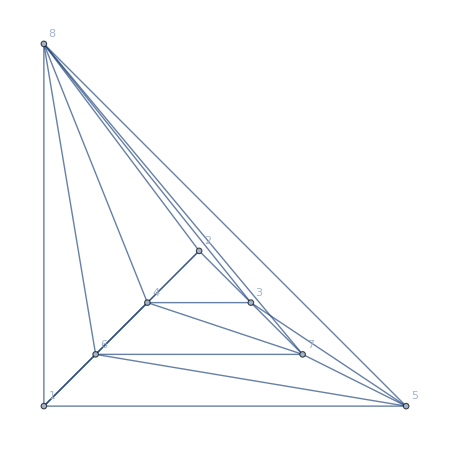
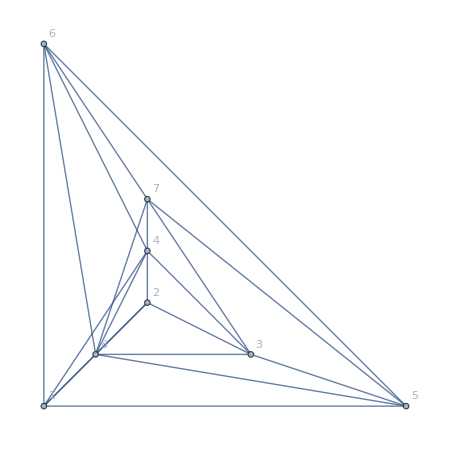
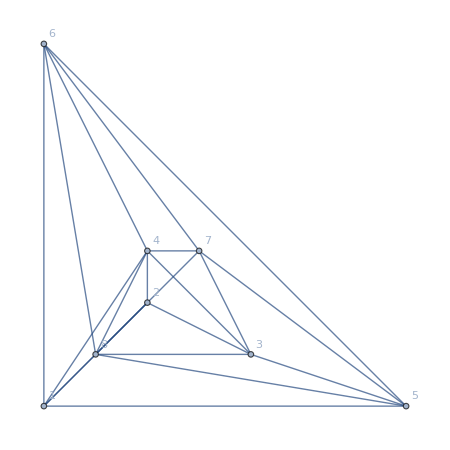
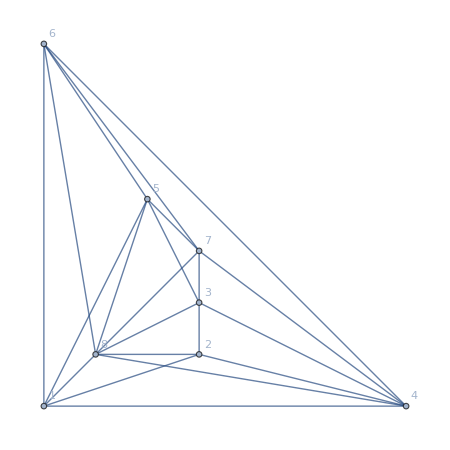
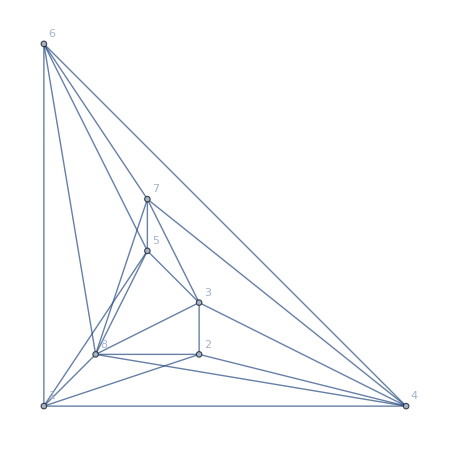
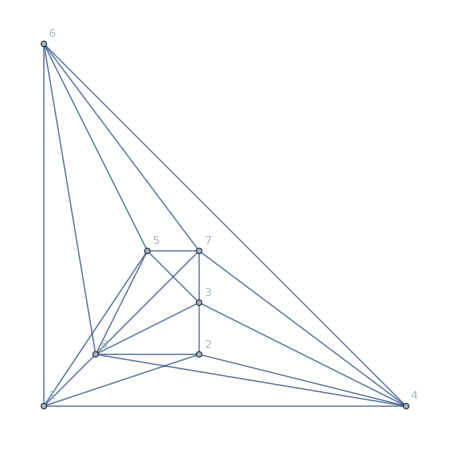
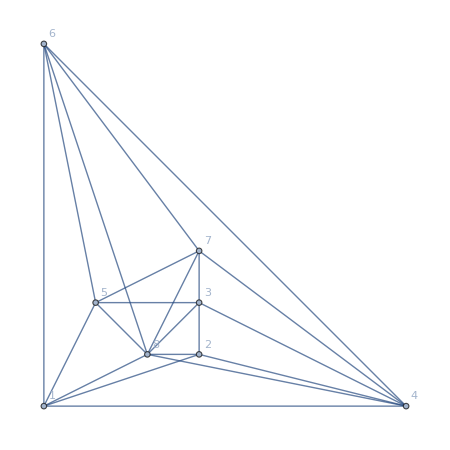
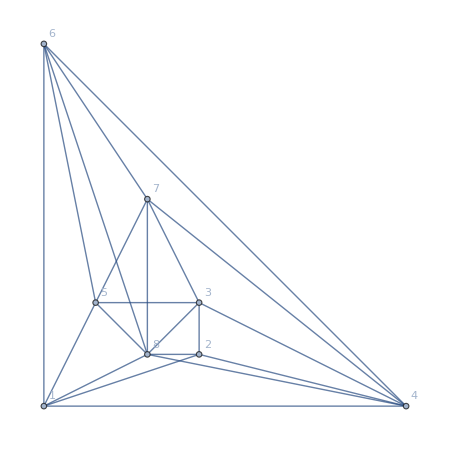
{-Graphics-{1<->2,1<->4,3<->5},-Graphics-{1<->2,1<->4,4<->6},-Graphics-{1<->2,1<->4,7<->8},-Graphics-{1<->2,1<->5,3<->5},-Graphics-{1<->2,1<->5,5<->6},-Graphics-{1<->2,1<->5,7<->8},-Graphics-{1<->2,3<->5,5<->7},-Graphics-{1<->2,3<->5,6<->8},-Graphics-{1<->2,6<->8,7<->8},-Graphics-{1<->5,1<->6,3<->5},-Graphics-{1<->5,1<->6,4<->6},-Graphics-{1<->5,1<->6,5<->6},-Graphics-{1<->5,1<->6,7<->8},-Graphics-{1<->5,2<->3,3<->4},-Graphics-{1<->5,2<->3,3<->5},-Graphics-{1<->5,2<->3,5<->6},-Graphics-{1<->5,2<->3,7<->8},-Graphics-{1<->5,3<->5,3<->7},-Graphics-{1<->5,3<->5,4<->8},-Graphics-{1<->5,4<->8,5<->6},-Graphics-{1<->5,4<->8,7<->8},-Graphics-{1<->5,5<->6,6<->7},-Graphics-{2<->3,3<->4,4<->7},-Graphics-{2<->3,3<->4,6<->8},-Graphics-{2<->3,3<->5,5<->7},-Graphics-{2<->3,3<->5,6<->8},-Graphics-{2<->3,6<->8,7<->8},-Graphics-{3<->5,3<->7,4<->7},-Graphics-{3<->5,3<->7,5<->7},-Graphics-{3<->5,3<->7,6<->8},-Graphics-{3<->5,4<->8,5<->7},-Graphics-{3<->5,4<->8,6<->8},-Graphics-{3<->5,5<->7,6<->7},-Graphics-{4<->8,6<->8,7<->8}}

{-Graphics-{1<->2,1<->4,3<->5},-Graphics-{1<->2,1<->4,4<->6},-Graphics-{1<->2,1<->4,7<->8},-Graphics-{1<->2,1<->5,3<->5},-Graphics-{1<->2,1<->5,5<->6},-Graphics-{1<->2,1<->5,7<->8},-Graphics-{1<->2,3<->5,5<->7},-Graphics-{1<->2,3<->5,6<->8},-Graphics-{1<->2,6<->8,7<->8},-Graphics-{1<->5,1<->6,3<->5},-Graphics-{1<->5,1<->6,4<->6},-Graphics-{1<->5,1<->6,5<->6},-Graphics-{1<->5,1<->6,7<->8},-Graphics-{1<->5,2<->3,3<->4},-Graphics-{1<->5,2<->3,3<->5},-Graphics-{1<->5,2<->3,5<->6},-Graphics-{1<->5,2<->3,7<->8},-Graphics-{1<->5,3<->5,3<->7},-Graphics-{1<->5,3<->5,4<->8},-Graphics-{1<->5,4<->8,5<->6},-Graphics-{1<->5,4<->8,7<->8},-Graphics-{1<->5,5<->6,6<->7},-Graphics-{2<->3,3<->4,4<->7},-Graphics-{2<->3,3<->4,6<->8},-Graphics-{2<->3,3<->5,5<->7},-Graphics-{2<->3,3<->5,6<->8},-Graphics-{2<->3,6<->8,7<->8},-Graphics-{3<->5,3<->7,4<->7},-Graphics-{3<->5,3<->7,5<->7},-Graphics-{3<->5,3<->7,6<->8},-Graphics-{3<->5,4<->8,5<->7},-Graphics-{3<->5,4<->8,6<->8},-Graphics-{3<->5,5<->7,6<->7},-Graphics-{4<->8,6<->8,7<->8}}

```mathematica
Table[With[{h=Graph[EdgeDelete[-Graphics-,e],GraphLayout->"PlanarEmbedding"]},Labeled[Graph[-Graphics-,EdgeStyle->Table[e[[k]]->Directive[Thickness[0.05],Opacity[0.3],{Red,Yellow,Blue}[[k]]],{k,Length[e]}],VertexCoordinates->GraphEmbedding[h],ImageSize->450],e]],{e,cross}]
```